## Un primer vistazo a las listas

Las listas son una forma básica de reunir una colección de cosas en Wolfram Language. {1,2,3} es una lista de números. Por sí mismas, las listas no hacen nada; son solo una forma de almacenar cosas. Así, si solo se ingresa una lista como entrada, la salida será lo mismo que se ingresó:

```mathematica
{1,2,3,4,a,b,c}
```

{1,2,3,4,a,b,c}

ListPlot es una función que produce la representación gráfica de una lista de números.

Construya un gráfico de la lista de números {1,1,2,2,3,4,4}:

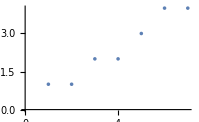

```mathematica
ListPlot[{1,1,2,2,3,4,4}]
```

Presente el gráfico de la lista de números {10,9,8,7,3,2,1}:

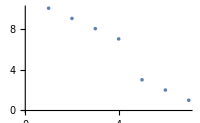

```mathematica
ListPlot[{10,9,8,7,3,2,1}]
```

Range es una función que produce una lista de números.

Genere una lista de números del 1 hasta el 10:

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

Genere una lista de números y luego preséntela gráficamente:

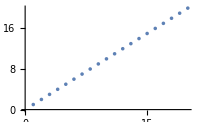

```mathematica
ListPlot[Range[20]]
```

Reverse invierte el orden de los elementos de una lista.

Invierta el orden de los elementos de una lista:

```mathematica
Reverse[{1,2,3,4}]
```

{4,3,2,1}

Invierta el orden en el resultado de Range:

```mathematica
Reverse[Range[10]]
```

{10,9,8,7,6,5,4,3,2,1}

Presente el gráfico de la lista con el orden invertido:

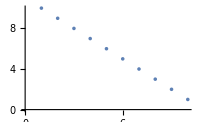

```mathematica
ListPlot[Reverse[Range[10]]]
```

Join junta varias listas, dando como resultado una sola.

Junte listas:

```mathematica
Join[{1,2,3},{4,5},{6,7}]
```

{1,2,3,4,5,6,7}

```mathematica
Join[{1,2,3},{1,2,3,4,5}]
```

{1,2,3,1,2,3,4,5}

Junte listas producidas por Range:

```mathematica
Join[Range[3],Range[5]]
```

{1,2,3,1,2,3,4,5}

Presente gráficamente tres listas empalmadas:

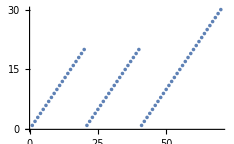

```mathematica
ListPlot[Join[Range[20],Range[20],Range[30]]]
```

Ponga al revés la lista del medio:

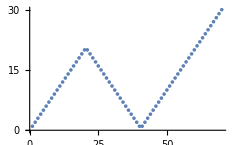

```mathematica
ListPlot[Join[Range[20],Reverse[Range[20]],Range[30]]]
```

Vocabulario

{1,2,3,4} |   | lista de elementos 
ListPlot[{1,2,3,4}] |   | presenta gráficamente una lista de números 
Range[10] |   | una secuencia de números consecutivos 
Reverse[{1,2,3}] |   | invierte el orden de una lista
Join[{4,5,6},{2,3,2}] |   | junta varias listas

"11 Exercises Available"
"with 5 extras" | "Get Started »"

Use Range para crear la lista {1,2,3,4}. »

| Expected output: |  
  | {1,2,3,4} |

Construya la lista de los números hasta el 100. »

| Expected output: |  
  | {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100} |

Use Range y Reverse para crear {4,3,2,1}. »

| Expected output: |  
  | {4,3,2,1} |

Construya la lista de los números del 1 al 50 en orden inverso. »

| Expected output: |  
  | {50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1} |

Use Range, Reverse y Join para crear {1,2,3,4,4,3,2,1}. »

| Expected output: |  
  | {1,2,3,4,4,3,2,1} |

Dibuje una lista que contenga los números del 1 al 100, seguidos de los números 99 al 1. »

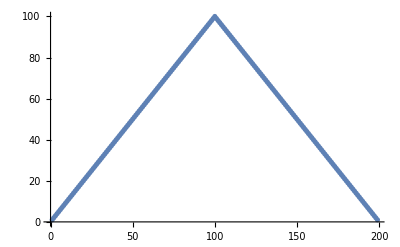
| Expected output: |  
  | -Graphics- |

Use Range y RandomInteger para crear una lista de longitud aleatoria hasta 10. »

| Sample expected output: |  
  | {1} |

Encuentre una forma más simple para Reverse[Reverse[Range[10]]]. »

| Expected output: |  
  | {1,2,3,4,5,6,7,8,9,10} |

Encuentre una forma más simple para Join[{1,2},Join[{3,4},{5}]]. »

| Expected output: |  
  | {1,2,3,4,5} |

Encuentre una forma más simple para Join[Range[10],Join[Range[10],Range[5]]]. »

| Expected output: |  
  | {1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5} |

Encuentre una forma más simple para Reverse[Join[Range[20],Reverse[Range[20]]]]. »

| Expected output: |  
  | {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1} |

Ponga en orden inverso la lista {1,2,3,4} y en orden inverso el resultado. »

| Expected output: |  
  | {1,2,3,4} |

Use Range, Reverse y Join para crear la lista {1,2,3,4,5,4,3,2,1}. »

| Expected output: |  
  | {1,2,3,4,5,4,3,2,1} |

Use Range, Reverse y Join para crear {3,2,1,4,3,2,1,5,4,3,2,1}. »

| Expected output: |  
  | {3,2,1,4,3,2,1,5,4,3,2,1} |

Dibuje el gráfico de la lista de números {10,11,12,13,14}. »

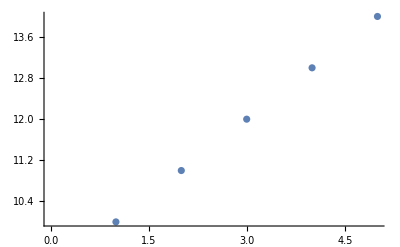
| Expected output: |  
  | -Graphics- |

Encuentre una forma más simple para Join[Join[Range[10],Reverse[Range[10]]],Range[10]]. »

| Expected output: |  
  | {1,2,3,4,5,6,7,8,9,10,10,9,8,7,6,5,4,3,2,1,1,2,3,4,5,6,7,8,9,10} |

Preguntas y respuestas

¿Cómo se lee en voz alta {1,2,3}?

Por lo regular, “lista 1 2 3”. “{” y “}” se llaman “llaves” o “paréntesis rizados”. “{” se dice “abrir llave” y “}” se dice “cerrar llave”.

¿Es una lista una función?

Sí. {1,2,3} es List[1,2,3]. Pero a diferencia de Plus, por ejemplo, la función List no realiza ninguna operación y en la salida aparece sin cambio.

¿Qué se representa gráficamente con ListPlot?

Los valores de elementos sucesivos. El valor x de cada punto da su posición en la lista; el valor y da el valor de ese elemento.

¿Qué tamaño puede llegar a tener una lista?

El que se quiera, con la única restricción de la memoria de la computadora.

Notas técnicas

Range[m,n] genera los números del m al n. Range[m,n,s] genera los números del m al n en incrementos de s.

Muchos lenguajes de computación tienen componentes lógicos como las listas (a menudo llamadas “arreglos”), aunque por lo general solo permiten listas de cosas explícitas, tales como números; no se puede tener una lista como {a,b,c} si no se ha dicho lo que son a, b y c. Sin embargo, en Wolfram Language sí se puede, debido a que Wolfram Language es simbólico.

{a,b,c} es una lista de elementos con un orden definido; {b,c,a} es una lista diferente.

Al igual que en las matemáticas, se pueden establecer teoremas sobre funciones de Wolfram Language. Por ejemplo, Reverse[Reverse[x]] es igual a x.

Para explorar más

Guía para listas en Wolfram Language »